## Уравнение Ван-дер-Поля

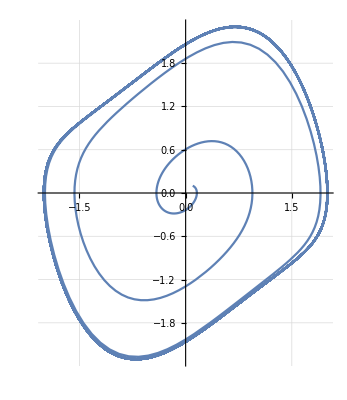

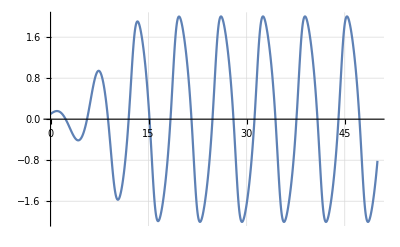

```mathematica
sol=NDSolveValue[{y''[t]-0.6y'[t](1-y[t]^2)+y[t]==0,y[0]==0.1,y'[0]==0.1},{y[t],y'[t]},{t,0,200}];
ParametricPlot[sol,{t,0,200},GridLines->Automatic]
Plot[sol[[1]],{t,0,50},GridLines->Automatic]
```

```mathematica
sol[[1]][1]
```

InterpolatingFunction[…][t][1]

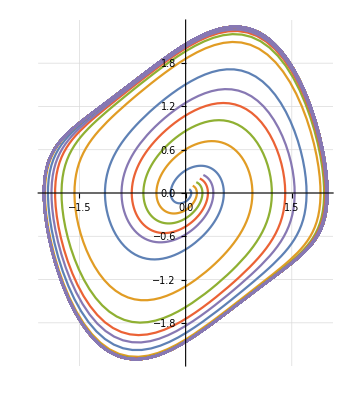

```mathematica
sols=Table[NDSolveValue[{y''[t]-0.6y'[t](1-y[t]^2)+y[t]==0,y[0]==0.05*i,y'[0]==0.05*i},{y[t],y'[t]},{t,0,200}],{i,1,5}];
ParametricPlot[sols,{t,0,200},GridLines->Automatic]
```

Неустойчивый фокус

### С++

Рунге-Кутты 4 порядка:

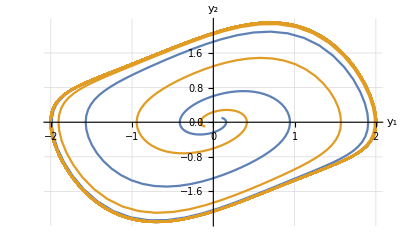

Симметричная схема:

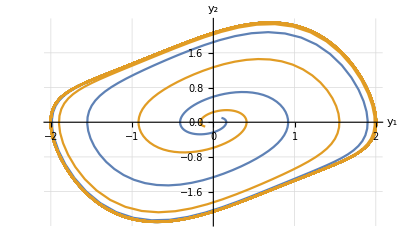

Неявный метод Эйлера:

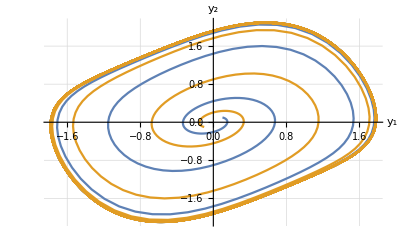

```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE"];
rk41=Import["part4_rk4_1.txt","Table"];
rk42=Import["part4_rk4_2.txt","Table"];
Print["Рунге-Кутты 4 порядка:"];
Print@ListLinePlot[{rk41,rk42},GridLines->Automatic,AxesLabel->{"y_1","y_2"}];
symm1=Import["part4_symm_1.txt","Table"];
symm2=Import["part4_symm_2.txt","Table"];
Print["Симметричная схема:"];
Print@ListLinePlot[{symm1,symm2},GridLines->Automatic,AxesLabel->{"y_1","y_2"}];
impl1=Import["part4_impl_1.txt","Table"];
impl2=Import["part4_impl_2.txt","Table"];
Print["Неявный метод Эйлера:"];
Print@ListLinePlot[{impl1,impl2},GridLines->Automatic,AxesLabel->{"y_1","y_2"}];
(*rk43=Import["part4_rk4_3.txt","Table"];
Print["Рунге-Кутты 4 порядка с внешней траекторией:"];
Print@ListLinePlot[{rk41,rk42,rk43},GridLines->Automatic,AxesLabel->{"y_1","y_2"}];*)
```

Тоже неустойчивый фокус